## Data Import

Import metadata such as the position of each of the feeding stations, water station and the corners of the paddock.

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

Create a Graphics Boundary of the paddock

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

Import the raw GPS data, so the X and Y coordinates as well as the time stamps and IDS.

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

The dataset has 51 sheep(+header) and 210352 time steps

```mathematica
Dimensions[rawXs]
```

{52,210352}

Create two versions of the coordinates, one with missing data as Missing[] for more computational tasks and one with missing data as “Indeterminate” for mathematical tasks

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate
```

{{{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},{Indeterminate,Indeterminate},210343,{582412.,6.56368×10^6},{582415.,6.56368×10^6},{582418.,6.56368×10^6},{Indeterminate,Indeterminate}},49,{1}}
 |  |  |  |

## Distribution of distances

### Individual Sheep

Function to determine the distance between sheep a and b

```mathematica
distances[a_,b_]:=Sqrt[Total[(rawCoordinates2[[a]] - rawCoordinates2[[b]])^2,{2}]]
```

Running this on two sheep will yield the distance they are from each other at each time step

```mathematica
distances[2,4]
```

{Indeterminate,6.2241,8.98001,13.3817,17.971,22.3762,28.6324,26.5542,210335,142.027,140.091,137.291,137.158,137.012,138.097,138.566,Indeterminate}
 |  |  |  |

Creates a function that for a given sheep and time finds all other sheep within a specified radius

```mathematica
SingleSheepWithinRadius[radius_,sheep_,time_]:=
If[rawCoordinates[[sheep,time]]==={Missing[],Missing[]},
Missing[],Nearest[DeleteMissing[MapIndexed[#1->#2[[1]]&,rawCoordinates[[All,time]]],1,3],rawCoordinates[[sheep,time]],{All,radius}]]
```

At step 3000, sheep 7 has 3 other sheep with it in less than 50m radius

```mathematica
SingleSheepWithinRadius[50,7,3000]
```

{7,49,12,32}

This allows us to

```mathematica
sheep1herdsize=With[{herd=SingleSheepWithinRadius[100,1,#]},If[MissingQ[herd],Missing[],Length[herd]]]&/@Range[Length[rawCoordinates[[4]]]];
```

24.4138

22

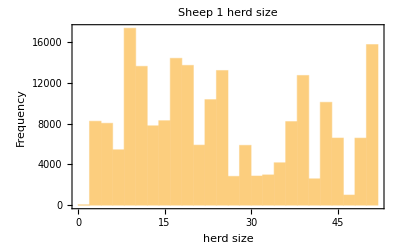

-Graphics-

```mathematica
Mean[DeleteMissing[sheep1herdsize]]//N
Median[DeleteMissing[sheep1herdsize]]
Histogram[sheep1herdsize,PlotLabel->"Sheep 1 herd size",Frame->True,FrameLabel->{"herd size","Frequency"}]
ListLinePlot[sheep1herdsize,PlotLabel->"Sheep 1 herd size over time",Frame->True,FrameLabel->{"time","herd size"}]
```

Set data Directory to export data to

### Mean over all sheep

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

Create a function that gets the distances for a pair of sheep and exports the list as an .mx file.

```mathematica
exportDistance[a_,b_]:=
Module[{distance,name},
distance=distances[a,b];
name=StringJoin[ToString[a],"and",ToString[b],".mx"];
Export[FileNameJoin[{dataDirectory,name}],distance]]
```

Generate a list of all the names of the files that were exported.

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}]
```

Import the data one by one and find the mean and median of each

```mathematica
Module[{currentPairData,data},
data=Table[
currentPairData=DeleteCases[Import[FileNameJoin[{dataDirectory,name}]],Indeterminate];
{Median[currentPairData],Mean[currentPairData]},
{name,Flatten[PairNames]}];
medians=data[[All,1]];
means=data[[All,2]];]
Export[FileNameJoin[{dataDirectory,"medians.mx"}],medians];
Export[FileNameJoin[{dataDirectory,"means.mx"}],means];
```

Median::rectn: Rectangular array of real numbers is expected at position 1 in Median[{Missing[]}].

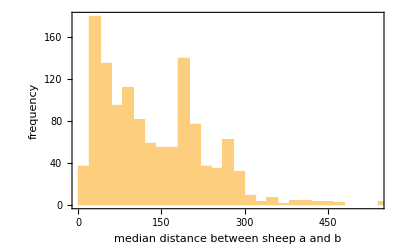

```mathematica
Histogram[medians,Frame->True,FrameLabel->{"median distance between sheep a and b","frequency"}]
```

### Sampling from all pairs

```mathematica
randomDistances=Select[Table[EuclideanDistance@@rawCoordinates2[[RandomInteger[{1,Length[rawCoordinates2]},2],RandomInteger[{1,Length[rawCoordinates2[[1]]]}]]],200000],#>0&]
```

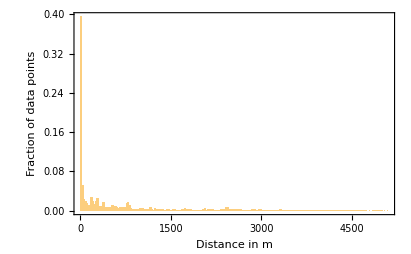

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->All]
```

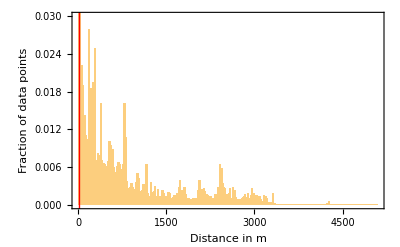

```mathematica
Histogram[randomDistances,{25},"Probability",Frame->True,FrameLabel->{"Distance in m","Fraction of data points"},PlotRange->{All,{0,0.03}},Epilog->{{Red,Thick,InfiniteLine[{{25,0},{25,1}}]}}]
```

```mathematica
Histogram[randomDistances,{50},Frame->True,FrameLabel->{"Distance","count"},ScalingFunctions->{"Log","Log"}]
```

```mathematica
feedingStationsDistances = DeleteCases[Flatten[DistanceMatrix[feeding]//N],0.];
```

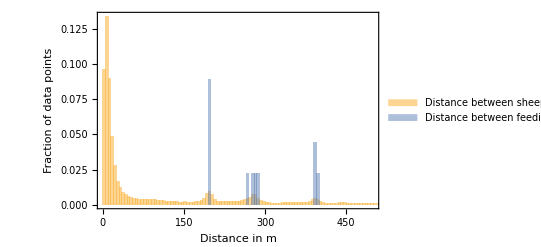

```mathematica
Histogram[{randomDistances,feedingStationsDistances},{5},"Probability",PlotRange->{{0,500},Automatic},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"},ChartLegends->{"Distance between sheep","Distance between feeding stations"}]
```

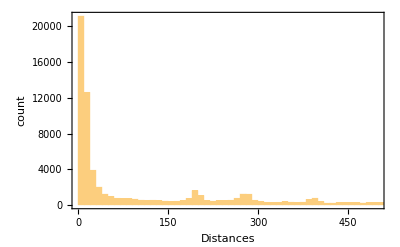

```mathematica
Histogram[randomDistances,{10},PlotRange->{{0,500},All},Frame->True,FrameLabel-> {"Distances","count"}]
```

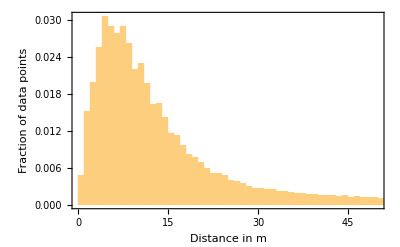

```mathematica
Histogram[randomDistances,{1},"Probability",PlotRange->{{0,50},All},Frame->True,FrameLabel-> {"Distance in m","Fraction of data points"}]
```

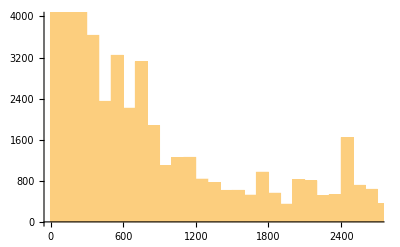

```mathematica
Histogram[randomDistances,PlotRange->{{0,2700},{0,4000}}]
```

## DBSCAN and Clustering